```mathematica
A=197; (*Pb*)
r0=6.38;(*fm*)
a=0.535 ;(*fm*)
σ=6.5;(*mb/10=fm^2, at √s=200GeV*)
ws[s_,z_]:=1/(A(1+Exp[(√(s^2+z^2)-r0)/a]));
ws1[s1_,s2_,ang_,z_]:=1/(A(1+Exp[(√(s1^2+s2^2-2s1 s2 Cos[ang]+z^2)-r0)/a]));
```

```mathematica
ρ0=1/NIntegrate[2π s ws[s,z],{s,0,∞},{z,-∞,∞}];
wsn[s_,z_]:=ρ0/(A(1+Exp[(√(s^2+z^2)-r0)/a]));
ws1n[s1_,s2_,ang_,z_]:=ρ0/(A(1+Exp[(√(s1^2+s2^2-2s1 s2 Cos[ang]+z^2)-r0)/a]));
```

```mathematica
T[s_]:=NIntegrate[wsn[s,z],{z,-∞,∞}]
T1[s1_,s2_,ang_]:=NIntegrate[ws1n[s1,s2,ang,z],{z,-∞,∞}]
TAA[b_]:=Quiet[NIntegrate[s T1[s,b,ang]T[s],{s,0,∞},{ang,0,2 π}]]
```

```mathematica
TAAtab=ParallelTable[{x,TAA[x]},{x,0,14,0.5}]
```

{{0.,0.00755886},{0.5,0.00751234},{1.,0.00737579},{1.5,0.00715744},{2.,0.00686881},{2.5,0.00652269},{3.,0.00613166},{3.5,0.00570736},{4.,0.00526028},{4.5,0.00479973},{5.,0.00433401},{5.5,0.00387051},{6.,0.00341587},{6.5,0.00297601},{7.,0.00255622},{7.5,0.00216116},{8.,0.00179489},{8.5,0.00146081},{9.,0.00116165},{9.5,0.000899401},{10.,0.000675182},{10.5,0.000489125},{11.,0.000340195},{11.5,0.000226026},{12.,0.000142858},{12.5,0.0000856988},{13.,0.0000488142},{13.5,0.0000264886},{14.,0.0000137697}}

```mathematica
TAAtab={{0.,0.007558864026676659},{0.5,0.007512344944835761},{1.,0.007375794206194003},{1.5,0.007157443030325738},{2.,0.006868813321135529},{2.5,0.006522687805327265},{3.,0.006131655042115531},{3.5,0.005707362588169074},{4.,0.005260280790053637},{4.5,0.004799730255244412},{5.,0.004334005125451636},{5.5,0.003870508969510548},{6.,0.003415867424987254},{6.5,0.0029760095747562586},{7.,0.0025562199284275447},{7.5,0.0021611637271957414},{8.,0.0017948888038114349},{8.5,0.0014608073847004327},{9.,0.0011616513707443988},{9.5,0.0008994009779430287},{10.,0.0006751822609073516},{10.5,0.0004891254220643536},{11.,0.00034019471318897623},{11.5,0.00022602561531308052},{12.,0.00014285813914476864},{12.5,0.00008569877804828624},{13.,0.00004881420258704518},{13.5,0.000026488575621041624},{14.,0.00001376971539148656}};
```

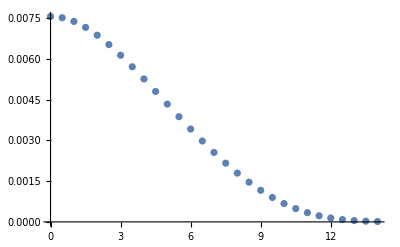

```mathematica
ListPlot[TAAtab]
```

```mathematica
TAAinter=Interpolation[TAAtab];
```

```mathematica
NIntegrate[2π x TAAinter[x],{x,0,14}]
```

0.999115

```mathematica
Quiet[NIntegrate[2π x T[x],{x,0,∞}]]
```

1.

```mathematica
Npart[b_]:=2 A Quiet[NIntegrate[s T1[s,b,ang](1-(1-σ T[s])^A),{s,0,∞},{ang,0,2 π}]];
```

```mathematica
Ncoll[b_]:=A^2 σ TAA[b];
```

```mathematica
Ncoll[0]
```

1906.79

```mathematica
NpartTab=Flatten[Join[{Table[{i,0},{i,0,2,0.1}],Table[{i,0},{i,2.5,12,0.5}],Table[{i,0},{i,12.1,15,0.1}]}],1]
SetSharedVariable[NpartTab];
```

{{0.,0},{0.1,0},{0.2,0},{0.3,0},{0.4,0},{0.5,0},{0.6,0},{0.7,0},{0.8,0},{0.9,0},{1.,0},{1.1,0},{1.2,0},{1.3,0},{1.4,0},{1.5,0},{1.6,0},{1.7,0},{1.8,0},{1.9,0},{2.,0},{2.5,0},{3.,0},{3.5,0},{4.,0},{4.5,0},{5.,0},{5.5,0},{6.,0},{6.5,0},{7.,0},{7.5,0},{8.,0},{8.5,0},{9.,0},{9.5,0},{10.,0},{10.5,0},{11.,0},{11.5,0},{12.,0},{12.1,0},{12.2,0},{12.3,0},{12.4,0},{12.5,0},{12.6,0},{12.7,0},{12.8,0},{12.9,0},{13.,0},{13.1,0},{13.2,0},{13.3,0},{13.4,0},{13.5,0},{13.6,0},{13.7,0},{13.8,0},{13.9,0},{14.,0},{14.1,0},{14.2,0},{14.3,0},{14.4,0},{14.5,0},{14.6,0},{14.7,0},{14.8,0},{14.9,0},{15.,0}}

```mathematica
NcollTab=Flatten[Join[{Table[{i,0},{i,0,2,0.1}],Table[{i,0},{i,2.5,12,0.5}],Table[{i,0},{i,12.1,15,0.1}]}],1]
SetSharedVariable[NcollTab]
```

{{0.,0},{0.1,0},{0.2,0},{0.3,0},{0.4,0},{0.5,0},{0.6,0},{0.7,0},{0.8,0},{0.9,0},{1.,0},{1.1,0},{1.2,0},{1.3,0},{1.4,0},{1.5,0},{1.6,0},{1.7,0},{1.8,0},{1.9,0},{2.,0},{2.5,0},{3.,0},{3.5,0},{4.,0},{4.5,0},{5.,0},{5.5,0},{6.,0},{6.5,0},{7.,0},{7.5,0},{8.,0},{8.5,0},{9.,0},{9.5,0},{10.,0},{10.5,0},{11.,0},{11.5,0},{12.,0},{12.1,0},{12.2,0},{12.3,0},{12.4,0},{12.5,0},{12.6,0},{12.7,0},{12.8,0},{12.9,0},{13.,0},{13.1,0},{13.2,0},{13.3,0},{13.4,0},{13.5,0},{13.6,0},{13.7,0},{13.8,0},{13.9,0},{14.,0},{14.1,0},{14.2,0},{14.3,0},{14.4,0},{14.5,0},{14.6,0},{14.7,0},{14.8,0},{14.9,0},{15.,0}}

```mathematica
Off[NIntegrate::inumr]
```

```mathematica
ParallelDo[NpartTab[[i,2]]=Npart[NpartTab[[i,1]]],{i,Length[NpartTab]}]//AbsoluteTiming
```

{1184.79,Null}

```mathematica
ParallelDo[NcollTab[[i,2]]=Ncoll[NcollTab[[i,1]]],{i,Length[NcollTab]}]//AbsoluteTiming
```

{1391.95,Null}

```mathematica
NpartTab
```

{{0.,384.773},{0.1,384.726},{0.2,384.587},{0.3,384.354},{0.4,384.026},{0.5,383.603},{0.6,383.083},{0.7,382.466},{0.8,381.749},{0.9,380.931},{1.,380.011},{1.1,378.987},{1.2,377.858},{1.3,376.622},{1.4,375.28},{1.5,373.83},{1.6,372.273},{1.7,370.608},{1.8,368.835},{1.9,366.956},{2.,364.972},{2.5,353.52},{3.,339.723},{3.5,323.923},{4.,306.494},{4.5,287.796},{5.,268.16},{5.5,247.886},{6.,227.244},{6.5,206.478},{7.,185.812},{7.5,165.455},{8.,145.603},{8.5,126.441},{9.,108.144},{9.5,90.881},{10.,74.8156},{10.5,60.1041},{11.,46.896},{11.5,35.3304},{12.,25.5255},{12.1,23.7836},{12.2,22.1157},{12.3,20.5221},{12.4,19.0027},{12.5,17.5574},{12.6,16.1859},{12.7,14.8876},{12.8,13.6619},{12.9,12.5077},{13.,11.424},{13.1,10.4093},{13.2,9.46205},{13.3,8.58031},{13.4,7.76208},{13.5,7.00511},{13.6,6.30696},{13.7,5.66507},{13.8,5.07673},{13.9,4.53912},{14.,4.04938},{14.1,3.60458},{14.2,3.20179},{14.3,2.83811},{14.4,2.51067},{14.5,2.2167},{14.6,1.95343},{14.7,1.7183},{14.8,1.50882},{14.9,1.32265},{15.,1.15756}}

```mathematica
NpartTab={{0.,384.7728519855433},{0.1,384.7263508701577},{0.2,384.5867433339151},{0.30000000000000004,384.3535394578965},{0.4,384.02594565602163},{0.5,383.6030048119073},{0.6000000000000001,383.0834676075236},{0.7000000000000001,382.4659696270717},{0.8,381.7489558324545},{0.9,380.93117913568767},{1.,380.01087950465956},{1.1,378.98676226961925},{1.2000000000000002,377.8575748742697},{1.3,376.622225263531},{1.4000000000000001,375.28000886743274},{1.5,373.8303130502087},{1.6,372.2728187006724},{1.7000000000000002,370.60769757912675},{1.8,368.8352889382444},{1.9000000000000001,366.95629143639457},{2.,364.97171797644626},{2.5,353.5198092012767},{3.,339.72251781821217},{3.5,323.92313277377315},{4.,306.4940051979294},{4.5,287.795842564727},{5.,268.16023347141555},{5.5,247.88638442775186},{6.,227.243923707622},{6.5,206.4776066634324},{7.,185.81195116011278},{7.5,165.45541223291002},{8.,145.6033786036931},{8.5,126.44070552220617},{9.,108.14359555228016},{9.5,90.881014038979},{10.,74.81561760560234},{10.5,60.104052653777565},{11.,46.89599320570524},{11.5,35.330374594729854},{12.,25.525454683360376},{12.1,23.783558429341433},{12.2,22.115699166070954},{12.299999999999999,20.522059344908953},{12.4,19.002661320913223},{12.5,17.557367904174736},{12.6,16.18585470928035},{12.7,14.887601920990983},{12.799999999999999,13.661881915278878},{12.9,12.507749062472968},{13.,11.424035016507377},{13.1,10.409342501594857},{13.2,9.462049597192294},{13.3,8.58031380966126},{13.4,7.76208256353183},{13.5,7.005107523572185},{13.6,6.306963877248374},{13.7,5.6650729591888185},{13.8,5.076727884087696},{13.9,4.539121679919598},{14.,4.049377185508544},{14.1,3.6045768793511743},{14.2,3.2017925201030866},{14.3,2.838113857708717},{14.4,2.5106749094015037},{14.5,2.2166973298629724},{14.6,1.9534340759438225},{14.7,1.718302846970007},{14.8,1.508823203607699},{14.9,1.3226467365184216},{15.,1.157564648905781}};
```

```mathematica
NcollTab
```

{{0.,1232.08},{0.1,1231.77},{0.2,1230.86},{0.3,1229.34},{0.4,1227.22},{0.5,1224.5},{0.6,1221.19},{0.7,1217.29},{0.8,1212.83},{0.9,1207.81},{1.,1202.24},{1.1,1196.13},{1.2,1189.5},{1.3,1182.37},{1.4,1174.75},{1.5,1166.65},{1.6,1158.09},{1.7,1149.09},{1.8,1139.66},{1.9,1129.83},{2.,1119.6},{2.5,1063.18},{3.,999.446},{3.5,930.288},{4.,857.414},{4.5,782.345},{5.,706.433},{5.5,630.884},{6.,556.779},{6.5,485.083},{7.,416.658},{7.5,352.265},{8.,292.563},{8.5,238.108},{9.,189.347},{9.5,146.6},{10.,110.053},{10.5,79.7264},{11.,55.451},{11.5,36.8417},{12.,23.2856},{12.1,21.1119},{12.2,19.1009},{12.3,17.2452},{12.4,15.537},{12.5,13.9687},{12.6,12.5326},{12.7,11.221},{12.8,10.0261},{12.9,8.94049},{13.,7.95661},{13.1,7.06723},{13.2,6.2653},{13.3,5.54401},{13.4,4.89685},{13.5,4.31758},{13.6,3.80029},{13.7,3.3394},{13.8,2.92966},{13.9,2.56619},{14.,2.24443},{14.1,1.96017},{14.2,1.70951},{14.3,1.48891},{14.4,1.29509},{14.5,1.12511},{14.6,0.976288},{14.7,0.846178},{14.8,0.732606},{14.9,0.633614},{15.,0.547449}}

```mathematica
Ncolltab={{0.,1232.0782068474368},{0.1,1231.7727293662679},{0.2,1230.859248630568},{0.30000000000000004,1229.3386569542204},{0.4,1227.2155649277813},{0.5,1224.4956988493504},{0.6000000000000001,1221.185953020914},{0.7000000000000001,1217.294603586564},{0.8,1212.832115207291},{0.9,1207.8092678349913},{1.,1202.238228862369},{1.1,1196.1321187254832},{1.2000000000000002,1189.5049484646072},{1.3,1182.3714562196678},{1.4000000000000001,1174.7470086231804},{1.5,1166.6474675684287},{1.6,1158.0891393984596},{1.7000000000000002,1149.088244453213},{1.8,1139.662457418436},{1.9000000000000001,1129.8277607758616},{2.,1119.601459955785},{2.5,1063.1837623551726},{3.,999.4462822237391},{3.5,930.2875456738652},{4.,857.4141961610048},{4.5,782.3454721982777},{5.,706.4333006373408},{5.5,630.8844469104865},{6.,556.7788753645875},{6.5,485.08301346420575},{7.,416.6582246498473},{7.5,352.26493297270605},{8.,292.56292626589556},{8.5,238.10838992992421},{9.,189.34661779832138},{9.5,146.60038072256222},{10.,110.05322312692432},{10.5,79.7263677205611},{11.,55.45098982143411},{11.5,36.84167803967844},{12.,23.285562392691173},{12.1,21.11191641400607},{12.2,19.10094228671289},{12.299999999999999,17.24516597367502},{12.4,15.536984960002032},{12.5,13.968712284558952},{12.6,12.532619589983497},{12.7,11.22098489486877},{12.799999999999999,10.026133803137336},{12.9,8.940488584932988},{13.,7.956607630442673},{13.1,7.067227005158699},{13.2,6.265296729113328},{13.3,5.544014114306378},{13.4,4.8968511388349585},{13.5,4.317579551363419},{13.6,3.8002880587053993},{13.7,3.339396333171773},{13.8,2.929664006867539},{13.9,2.5661941773571413},{14.,2.244433315438448},{14.1,1.9601669103319692},{14.2,1.7095118500762858},{14.3,1.4889056001144176},{14.4,1.2950935511342154},{14.5,1.1251139376664634},{14.6,0.9762880146890299},{14.7,0.8461778932752313},{14.8,0.7326064041851661},{14.9,0.6336143477405426},{15.,0.5474491077535242}};
```

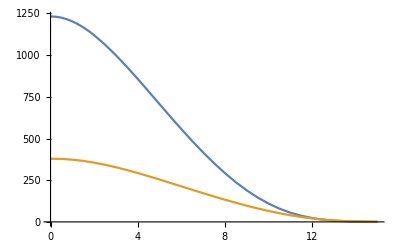

```mathematica
ListPlot[{NcollTab,NpartTab},Joined->True]
```